## Lecture 3a. Eigenproblems.

## Eigenvalues and eigenvectors of the matrices.

### Symbolic computations of eigenvalues and eigenvectors

Spectral properties of the matrix are found with the help of functions  and   (they can be evaluated simultaneously with ).

```mathematica
σ[n_]=PauliMatrix[n];
(H = Sin[θ]Cos[ϕ] σ[1]+ Sin[θ]Sin[ϕ] σ[2]+ Cos[θ] σ[3])//FullSimplify//MatrixForm
```

(Cos[θ] | ⅇ^(-ⅈ ϕ) Sin[θ]
ⅇ^(ⅈ ϕ) Sin[θ] | -Cos[θ])

```mathematica
Eigenvalues[H]
```

```mathematica
U=Eigenvectors[H]//FullSimplify
```

Let me check, that these are truly eigen vectors of the matrix H.

```mathematica
Array[H.Eigenvectors[H][[#]]==Eigenvalues[H][[#]]Eigenvectors[H][[#]]&,2]//FullSimplify
```

If you want vectors to have unit norm, use  function.

```mathematica
MatrixForm/@(FullSimplify[Normalize/@Eigenvectors[H],Assumptions->{ϕ∈Reals,0<θ<π}])
```

NB! Since  returns a list of (co)vectors, change-of-the-basis matrix is given by  matrix.

```mathematica
Clear[U];(U=(Eigenvectors@H)ᵀ//FullSimplify)//MatrixForm
```

```mathematica
Inverse[U].H.U//Simplify//MatrixForm
```

#### Example: Dirac Hamiltonian.

```mathematica
Clear["`*"];
α[0]=KroneckerProduct[PauliMatrix[3],PauliMatrix[0]];
α[n_]:=KroneckerProduct[PauliMatrix[1],PauliMatrix[n]]/;1≤n≤ 3&&IntegerQ[n]
H=k1 α[1] + k2 α[2] + k3 α[3] + m α[0];
Echo[H//MatrixForm,"H = "];
Echo[Eigenvalues[H],"Λ(H): "];
Plot[Evaluate[Normal@Eigenvalues[H]//.{k1^2+k2^2+k3^2->k^2,m->1}],{k,-3,3},AxesLabel->{"|k|/m","ϵ[k]/m"},PlotLegends->Array[StringTemplate["ϵ_(``)"][#]&,4],PlotStyle->{{Blue},{Yellow,AbsoluteDashing[{10,15}]},Red,{Green,AbsoluteDashing[{10,15}]}}]
```

### Approximate numerical computations

If you don’t want  to produce an exact expressions for eigen values and eigen vectors you simply need to consider a matrix with finite (not symbolic ∞) precision. 
Note: The following code doesn’t work in about 1% of all cases when randomized integer matrix is singular. If you have got an error message from , consider yourself lucky.

```mathematica
U=RandomInteger[2,{10,10}];
H=Evaluate[Inverse[U].DiagonalMatrix[Array[#&,10,{-5,4}]].U];
```

```mathematica
Eigensystem[H][[1]]//AbsoluteTiming
Eigensystem[1.H][[1]]//AbsoluteTiming
```

#### Exercise 3.1

Find largest and smallest eigenvalue and corresponding eigenvector of the defined before matrix H (automatize the process).

#### Solution 3.1

```mathematica
Λ=Eigenvalues[H];λmin=Min[Λ];λmax=Max[Λ];
Print[{λmin,λmax}];
MatrixForm/@{Vmin=Eigenvectors[H][[Position[Λ,λmin][[1,1]]]],
Vmax=Eigenvectors[H][[Position[Λ,λmax][[1,1]]]]}
```

#### Solution 3.1*

The following function works as Eigensystem, but sorts outputs by eigenvalues.

```mathematica
OrderedEigensystem[mat_,n_]:=With[{es=Eigensystem[mat]},With[{m=esᵀ,o=Ordering[First@es,-n]},First@m[[o]]]];
OrderedEigensystem[1.H,1]
OrderedEigensystem[1.H,-1]
```

### The largest and smallest eigenvalue

Since we are usually interested in beginning or the end of the spectrum, it would be helpful to find the ends of the spectrum without finding it whole.

Naturally, for the largest and smallest eigenvalues accordingly we call

```mathematica
Eigensystem[H,1]
Eigensystem[H,-1]
```

But! As you may have noticed, the results are order by their absolute value, which is not what we expected. Another misfortune is that such function call is not time-effective (for both symbolic and numeric calculations), since [H, n] is equivalent to [#, n] & /@ [H]. You can check it using . So if you want eigenvalues to be ordered as numbers with sign, use something like  function written above.

However, in case of real symmetric (non-symbolic) matrix, one can find eigenvalues with largest and smallest real parts, specifying the method of calculation.

```mathematica
U=Orthogonalize@RandomInteger[2,{10,10}];
H=Evaluate[Inverse[U].DiagonalMatrix[Array[#&,10,{-5,4}]].U];
```

```mathematica
Eigensystem[1.H,2,Method->{"Arnoldi","Criteria"->"BothEnds"}]//Chop//AbsoluteTiming
```

```mathematica
ClearAll["Global`*"]
```

#### Example: Kitaev model.

Let me explore the following Hamiltonian, that has quite important meaning in quantum computing and solid state physics.

H = -μ∑_(l=1)^L (a_l†.a_l-1/2)-w∑_(l=1)^(L-1) a_l†.a_(l+1)+a_(l+1)†.a_l+∑_(l=1)^(L-1) Δ a_l.a_(l+1)+Δ^*a_(l+1)†.a_l†,

where μ, w and Δ are some parameters.

```mathematica
Clear["`*"];L=6;
c[n_?IntegerQ]:=KroneckerProduct@@Join[Array[PauliMatrix[3]&,L-n],{{{0,1},{0,0}}},Array[IdentityMatrix[2]&,n-1]]/;1≤n≤L;
H=-μ Sum[c[n]†.c[n]-1/2 IdentityMatrix[2^L],{n,1,L}]-w Sum[c[n]†.c[n+1]+c[n+1]†.c[n],{n,1,L-1}]+Δ Sum[c[n].c[n+1]+c[n+1]†.c[n]†,{n,1,L-1}];
Λ[ω_?NumericQ]:=Sort@Eigenvalues[H/.{μ->1.,Δ->ω,w->ω}]//Chop;
(*Echo[H//MatrixForm,"H = "];*)
```

Let’s look at the many-body spectrum.

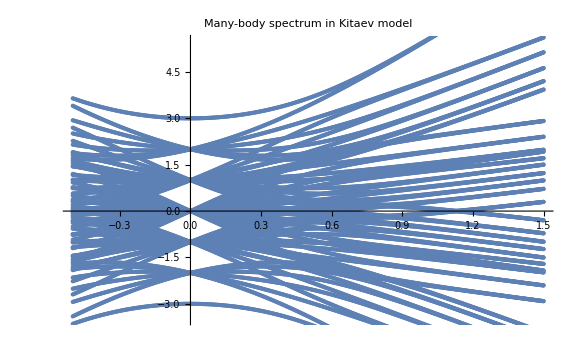

```mathematica
Show[Table[ListPlot[Replace[Λ[i],x_->{i,x},1],PlotStyle->PointSize[Small],PlotStyle->{Red,Blue,Green, Yellow}],{i,-.5,1.5,.004}],PlotRange->{-3.5,5.5},ImageSize->Large,AxesLabel->{"w/μ"},PlotLabel->"Many-body spectrum in Kitaev model"]
```

It’s main feature is following: when chain length L is large enough, namely ⅇ^(-L Log[w/μ])<<1, then there exist two “topologically” distinct phases. When w/μ>1/2 (and Δ≠0) one can introduce majorana operators, which leads to double-degeneracy of each many-body energy level. In the phase w/μ<1/2 levels are intermixed and for w=Δ=0 degeneracies are given by Pascal numbers determined by chain size L.

```mathematica
Tally@Λ[0.]
```

```mathematica
Clear["`*"];
```

## Schrödinger (Sturm-Liouville) problem

### DEigensystem

Eigen problem can be formulated in terms of differential operators. 
E.g. let’s look at the so-called Quantum Harmonic Oscillator operator. The problem is to find all such numbers λ and functions ψ[x] that satisfy

-ψ''[x]+x^2 ψ[x]==λ ψ[x];ψ[∞]==0;ψ[-∞]=0;

In such a simple case  can do it analytically via  function.

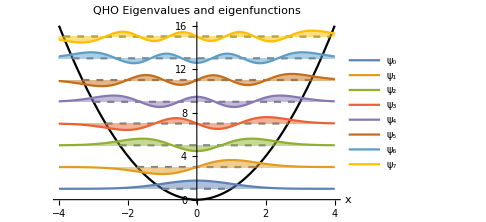

```mathematica
{QHOvals,QHOfuns}=DEigensystem[-ψ''[x]+x^2 ψ[x],ψ[x],{x,-∞,∞},10];
```

Function  can be used to solve harmonic oscillator and particle in a box (in different dimensions). For anything more complicated, you need a numerical solution given by .

### NDEigensystem

Let’s put an oscillator in a a box, i.e. change boundary conditions, and look how it will affect the eigenvalues.

-ψ''[x]+x^2 ψ[x]==λ ψ[x]; ψ[3.5]==0;ψ[-3.5]=0;

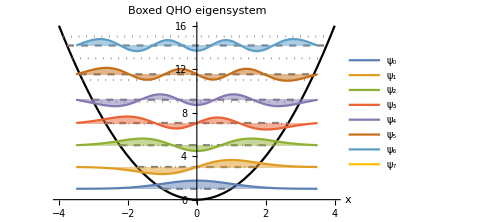

```mathematica
{NBQHOvals,NBQHOfuns}=NDEigensystem[{-Laplacian[u[x],{x}]+x^2 u[x],DirichletCondition[u[x]==0,True]},u[x],{x,-3.5,3.5},8];
```

From this example we learn that lowest part of the spectrum is slightly different from true oscillator and highest part is similar to particle in a box.

#### Visualizations

```mathematica
Show[Plot[{x^2},{x,-4,4},PlotStyle->{Black,Thick},AxesStyle->Directive[18],ImageSize->Medium,AxesLabel->{"x"},PlotLabel->Style["QHO Eigenvalues and eigenfunctions",Directive[18]]],
Plot[{Evaluate@Table[Piecewise[{{QHOvals[[n]],x^2<QHOvals[[n]]}},True],{n,1,8}]},{x,-4,4},PlotStyle->{{Dashed,Gray}}],
Plot[Evaluate@Table[QHOfuns[[n]]/(√Integrate[Abs[QHOfuns[[n]]]^2,{x,-∞,∞}])+QHOvals[[n]],{n,1,8}],{x,-4,4},Filling->Table[n->QHOvals[[n]],{n,1,8}],FillingStyle->Opacity[.5],PlotLegends->Array[Subscript[ψ, #-1]&,8]]
]
```

```mathematica
Show[Plot[{x^2},{x,-4,4},PlotStyle->{Black,Thick},AxesStyle->Directive[18],ImageSize->Medium,AxesLabel->{"x"},PlotLabel->Style["Boxed QHO eigensystem",Directive[18]]],
Plot[{Evaluate@Table[Piecewise[{{NBQHOvals[[n]],x^2<NBQHOvals[[n]]}},True],{n,1,8}]},{x,-4,4},PlotStyle->{{Dashed,Gray}}],
Plot[{Evaluate@Table[Piecewise[{{QHOvals[[n]],x^2<QHOvals[[n]]}},True],{n,1,8}]},{x,-4,4},PlotStyle->{{Dotted,Gray}}],
Plot[Evaluate@Table[NBQHOfuns[[n]]/(√NIntegrate[Abs[NBQHOfuns[[n]]]^2,{x,-3.5,3.5}])+NBQHOvals[[n]],{n,1,8}],{x,-4,4},Filling->Table[n->NBQHOvals[[n]],{n,1,8}],FillingStyle->Opacity[.5],PlotLegends->Array[Subscript[ψ, #-1]&,8]]
]
```

### ParametricNDSolve

Such function as  are actually appeared only in the latest version of . There are other methods on how to solve differential eigenproblems. Let me consider an example of Quartic Oscillator. I’m going to exploit the fact that such potential has a definite parity, and rephrase a boundary problem in terms of two (even, odd) initial problems.

```mathematica
ClearAll["`*"];
```

```mathematica
V[x_]:=x^4;
efuns=ParametricNDSolveValue[{-ψ''[x]+V[x] ψ[x]==λ ψ[x],ψ[0]==1,ψ'[0]==0},ψ,{x,-10,10},{λ}];
ofuns=ParametricNDSolveValue[{-ψ''[x]+V[x] ψ[x]==λ ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,-10,10},{λ}];
```

We have just found solutions for all possible values of λ. Let’s look at it. It blows up for large x.

```mathematica
Plot[{V[x],Evaluate@efuns[1.06][x]},{x,-4.8,4.8},Filling->{1-> 0},PlotRange->{-.5,1.5}]
```

We need to determine such λ, that solution decreases at ∞. Do that exactly is not possible, because of the finite precision of the solution. So let me pretend that ∞=4.

```mathematica
ϵ[0]=NMinimize[Abs[Evaluate@efuns[λ][4.]],{λ,1,1.1},WorkingPrecision->32][[2,1,2]];Echo[NumberForm[ϵ[0],16],"ϵ_0 = "];
Plot[{V[x],Evaluate@efuns[ϵ[0]][x]},{x,-4.8,4.8},Filling->{1-> 0},PlotRange->{-.5,1.5}]
```

### Matrix method

Another way to approach the problem is to write differential operator in in some appropriate basis, but cut it off on the finite number of elements, i.e. consider only several function from basis. It is usually convenient to choose Hermite (harmonic oscillator) basis.

```mathematica
Block[{X,P,M},
M=24;P=1/(√2)(DiagonalMatrix[Table[√m,{m,1,M}],-1]- DiagonalMatrix[Table[√m,{m,1,M}],1]);
X=1/(√2)(DiagonalMatrix[Table[√m,{m,1,M}],-1]+DiagonalMatrix[Table[√m,{m,1,M}],1]);
H=-P.P+X.X.X.X;
];
```

Now I want to find lowest eigenvalue and corresponding eigenvector.

```mathematica
Clear[evals,evects,OrderedEigensystem];
OrderedEigensystem[mat_,n_]:=With[{es=Eigensystem[mat]},With[{m=esᵀ,o=Ordering[First@es,-n]},First@m[[o]]]];
{evals,evects}=OrderedEigensystem[1.H,-1]//Chop;
```

The finite-size vector I have obtained consists of coefficients of expansion of ground state function into the Hermite functions.

```mathematica
χ[n_,x_]:=1/π^(1/4)HermiteH[n,x]/(E^(x^2/2)Sqrt[2^n n!]);
ψ[0,x_?NumericQ]:=-Sum[evects[[n+1]]χ[n,x],{n,0,24}];
Plot[{ψ[0,x],ψ[0,0] Exp[-x^2/2]},{x,-5,5},PlotStyle->{Blue,{Red,Dashed}}]
```

Finally, let’s compare exact energies with WKB approximation. We’ll see that all levels except the ground state fit pretty well.

```mathematica
WKBevals=N@Table[((3π √(2π))/Gamma[1/4]^2(n+1/2))^(4/3),{n,0,15}];
evals=Eigenvalues[1. H,-15];
```

```mathematica
Show[Plot[{x^4},{x,-2,2},PlotStyle->{Black,Thick},AxesStyle->Directive[16],ImageSize->Medium],
Plot[{Evaluate@Table[Piecewise[{{evals[[n]],x^4<evals[[n]]}},True],{n,0,15}]},{x,-2,2},PlotStyle->{{Dashed,Red}}],
Plot[{Evaluate@Table[Piecewise[{{WKBevals[[n]],x^4<WKBevals[[n]]}},True],{n,0,15}]},{x,-2,2},PlotStyle->{{Dashed,Blue}}]
]
```

#### Example. Landau Levels in Dirac system

## Problems

#### Problem 3.1

Consider a Pöschl–Teller potential (from the fluctuation determinant in double--well energy splitting problem).

-ψ''[x]+ψ[x]-3/2 ψ[x]/Cosh[x]^2==λ ψ[x]; ψ[∞]==0;ψ[-∞]=0;

That problem has a simple solutions.

ϵ[0]=0;ϵ[1]=3/4;ψ[0,x]=√(3/8)Sech[x/2]^2;ψ[1,x]=√(3/4)Sinh[x/2]Sech[x/2]^2;

0. Can  find these solutions?
1. Find, numerically, its eigenvalues and eigenfunctions, using .
2. Find, numerically, its eigenvalues and eigenfunctions, using .
3. Find, numerically, its eigenvalues and eigenfunctions, using finite matrix representation in Hermite basis.
Compare the results between each other and with the exact ones.